```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec. 3.4 lattice mismatch base on -Graphics-

## AA stacking hexagon Eq. S9

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0&&r>0&&as>0&&0≤θ≤π/3&&p≥0&&-1<δ<1&&x∈Reals&&y∈Reals&&as>0
```

R>0&&r>0&&as>0&&0≤θ≤π/3&&p≥0&&-1<δ<1&&x∈ℝ&&y∈ℝ&&as>0

```mathematica
fAA[x_,y_,λ_]=  Cos[(4 π x)/(√3 λ)]+2 Cos[(2  π x)/(√3 λ)] Cos[(2  π y)/λ]
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fAA[x_,y_,λ_]=fAA[x Cos[π/2]-y Sin[π/2],y Cos[π/2]+x Sin[π/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π x)/λ] Cos[(2 π y)/(√3 λ)]+Cos[(4 π y)/(√3 λ)]

```mathematica
γ=ArcCos[(Cos[θ]-p)/Sqrt[1+p^2-2p Cos[θ]]]
```

ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]

```mathematica
β=γ-θ;
```

```mathematica
ftheta[x_,y_,λ_,θ_,p_]=fAA[x Cos[-β]-y Sin[-β],y Cos[-β]+x Sin[-β],λ]  (*rotate anticlockwisely by γ-θ *)
```

Cos[(4 π (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)]+2 Cos[(2 π (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)] Cos[(2 π (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/λ]

```mathematica
λ=p Rs/(1+p^2-2 p Cos[θ])^(1/2)
```

(p Rs)/(√(1+p^2-2 p Cos[θ]))

```mathematica
f0[x_,y_,Rs_,θ_,p_]=Simplify[ftheta[x,y,λ,θ,p]]
```

Cos[(4 π √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)]+2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)] Cos[(2 π √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)]

```mathematica
nRf0[x_,y_,R_,Rs_,θ_,p_]=f0[x R,y R,Rs,θ,p]
```

Cos[(4 π √(1+p^2-2 p Cos[θ]) (R y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+R x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)]+2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (R y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+R x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)] Cos[(2 π √(1+p^2-2 p Cos[θ]) (R x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-R y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)]

```mathematica
nRnasnareauf0[x_,y_,θ_,r_,p_]=Simplify[nRf0[x,y,r*Rs*p,Rs,θ,p]]
```

Cos[(4 π r √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3)]+2 Cos[(2 π r √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3)] Cos[2 π r √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]

```mathematica
hexagonarea=Integrate[Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}]
```

(3 √3)/2

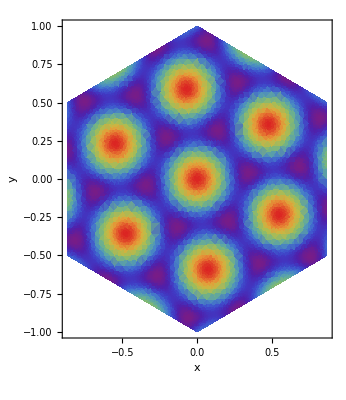

```mathematica
DensityPlot[nRnasnareauf0[x,y,2Degree,10Sqrt[3],1.09],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
NEhex[θ_,r_,p_]=Integrate[nRnasnareauf0[x,y,θ,r,p]Boole[-Sqrt[3]*x/3-1<y&&y<Sqrt[3]*x/3+1&&Sqrt[3]*x/3-1<y&&y<-Sqrt[3]*x/3+1],{x,-Sqrt[3]/2,Sqrt[3]/2},{y,-1,1}] ;
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

time used 6.42648678 mins

```mathematica
t1=AbsoluteTime[];
AAhex[θ_,r_,p_]=Simplify[NEhex[θ,r,p]/hexagonarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

-(((-1+3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^2) (6 √3 (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) Cos[(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-3 √3 Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-6 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-2 √3 Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]-4 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]-3 Cot[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+6 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cot[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+6 Csc[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+12 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Csc[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+2 √3 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+4 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-3 Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-6 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] (-√3+Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])))/(4 √3 π^2 r^2 (1+p^2-2 p Cos[θ]) (-1+2 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) (-1+√3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]) (1+√3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])))

time used 1.20936727 mins

```mathematica
A1[θ_,p_,r_]:=θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
```

```mathematica
A2[θ_,p_,r_]:=θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
```

```mathematica
B1[θ_,p_,r_]:=θ-ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
B2[θ_,p_,r_]:=θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
CC[θ_,p_,r_]:=2 π r √(1+p^2-2 p Cos[θ]) Cos[A1[θ,p,r]]/√3
```

```mathematica
D1[θ_,p_,r_]:=2 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[A1[θ,p,r]]+3Sin[A1[θ,p,r]])/3
D2[θ_,p_,r_]:=2 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[A1[θ,p,r]]-3Sin[A1[θ,p,r]])/3
```

```mathematica
EE[θ_,p_,r_]:=2π r(-1+p Cos[θ])/√3
```

```mathematica
F[θ_,p_,r_]:=Sin[2 π p r Sin[θ]]
```

```mathematica
G[θ_,p_,r_]:=2 π r √(1+p^2-2 p Cos[θ]) Sin[A1[θ,p,r]]
```

```mathematica
H[θ_,p_,r_]:=4 √3 π^2 r^2 (1+p^2-2 p Cos[θ])(-1+2Cos[2A1[θ,p,r]])(1+2Cos[2B2[θ,p,r]])(-1+3(Tan[A1[θ,p,r]]^2))
```

```mathematica
SumAAhex[θ_,p_,r_]=-(-1+3 Tan[A1[θ,p,r]]^2)/H[θ,p,r]*(6 √3(1+2Cos[2B2[θ,p,r]])Cos[2 CC[θ,p,r]]-3 √3 Cos[D1[θ,p,r]]-6 √3 Cos[2B2[θ,p,r]]Cos[D1[θ,p,r]]-√3 Sin[EE[θ,p,r]]F[θ,p,r]-2 √3 Cos[2B2[θ,p,r]]Sin[EE[θ,p,r]]F[θ,p,r]-3Cot[B2[θ,p,r]]Sin[EE[θ,p,r]]F[θ,p,r]+6Cos[2A1[θ,p,r]]Cot[B2[θ,p,r]]Sin[EE[θ,p,r]]F[θ,p,r]+6Csc[B2[θ,p,r]]Sin[A1[θ,p,r]]Sin[EE[θ,p,r]]F[θ,p,r]+12Cos[2B2[θ,p,r]]Csc[B2[θ,p,r]]Sin[A1[θ,p,r]]Sin[EE[θ,p,r]]F[θ,p,r]+√3 Sin[CC[θ,p,r]]Sin[G[θ,p,r]]+2 √3 Cos[2B2[θ,p,r]]Sin[CC[θ,p,r]]Sin[G[θ,p,r]]-3Cos[D1[θ,p,r]]Tan[A1[θ,p,r]]-6Cos[2B2[θ,p,r]]Cos[D1[θ,p,r]]Tan[A1[θ,p,r]]+3Sin[CC[θ,p,r]]Sin[G[θ,p,r]]Tan[A1[θ,p,r]]+6Cos[2B2[θ,p,r]]Sin[CC[θ,p,r]]Sin[G[θ,p,r]]Tan[A1[θ,p,r]]+3(1+2Cos[2B2[θ,p,r]])Cos[D2[θ,p,r]](-√3+Tan[A1[θ,p,r]]))
```

((1-3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^2) (6 √3 (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) Cos[(4 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-3 √3 Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-6 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]-√3 Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]-2 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]-3 Cot[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+6 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cot[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+6 Csc[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+12 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Csc[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-1+p Cos[θ]))/(√3)] Sin[2 p π r Sin[θ]]+√3 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]+2 √3 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]]-3 Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-6 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+6 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[(2 π r √(1+p^2-2 p Cos[θ]) Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)] Sin[2 π r √(1+p^2-2 p Cos[θ]) Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+3 (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) Cos[2/3 π r √(1+p^2-2 p Cos[θ]) (√3 Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-3 Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])] (-√3+Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])))/(4 √3 π^2 r^2 (1+p^2-2 p Cos[θ]) (-1+2 Cos[2 (θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) (1+2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]) (-1+3 Tan[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]^2))